# Solutions of Mathematica based Questions for Assignment 1, MATH7501, Sem 1, 2021

### Question 2 c

```mathematica
Sum[k^2,{k,1,n}]
```

1/6 n (1+n) (1+2 n)

```mathematica
2 n^3+3n(n+1)-2n //Simplify
```

n (1+3 n+2 n^2)

### Question 2 d

```mathematica
expr = 2(i-j) (n(n+1))/2-4(n(n+1)(2n+1))/6+n i j;
FullSimplify[expr]
```

i j n+(i-j) n (1+n)-2/3 n (1+n) (1+2 n)

```mathematica
check = Table[ 2(i-j) (n(n+1))/2-4(n(n+1)(2n+1))/6+n i j /.n->2,{i,1,3},{j,1,4}];
check //MatrixForm
```

(-18 | -22 | -26 | -30
-10 | -12 | -14 | -16
-2 | -2 | -2 | -2)

### Question 2 c

```mathematica
SeedRandom[1]
randM[r_]:=Table[RandomInteger[{1,r}],{3},{3}]
```

```mathematica
randCommuteTrial[r_]:=Module[{},
A = randM[r];
B = randM[r];
If[A.B == B.A,1,0]
]
```

```mathematica
n= 10^5;
est[r_]:= N[Total[Table[randCommuteTrial[r],{n}]]/n ]
```

```mathematica
Table[{r,est[r]},{r,2,5}] //TableForm
```

2 | 0.00333
3 | 0.00007
4 | 0.00002
5 | 0.

### Question 5 a

```mathematica
xVals = {2.4,4.7,4.9,2.9,8.1};
y = {3.1,2.7,4.8,7.6,5.4};
A = Table[If[j==1,1,xVals[[i]]],{i,1,5},{j,1,2}];
A //MatrixForm
```

(1 | 2.4
1 | 4.7
1 | 4.9
1 | 2.9
1 | 8.1)

```mathematica
β = {0,0};
bestNorm = ∞;
Do[
βtry = {RandomReal[{0,5}],RandomReal[{0,5}]};
norm = Norm[A.βtry-y];
If[norm < bestNorm, 
β = βtry;
bestNorm = norm;
Print["New best norm: ", bestNorm];
];
,10^6]
```

New best norm: 28.1809

New best norm: 5.6241

New best norm: 5.07316

New best norm: 3.94038

New best norm: 3.93268

New best norm: 3.93114

New best norm: 3.92946

New best norm: 3.9283

New best norm: 3.92825

New best norm: 3.92817

New best norm: 3.92816

New best norm: 3.92815

```mathematica
β
```

{4.52278,0.0436704}

```mathematica
f[x_]:=β[[1]]+β[[2]]x
```

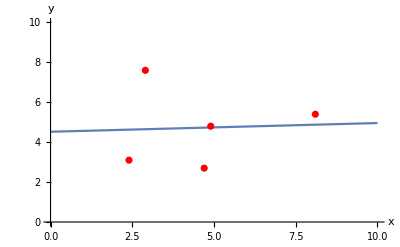

```mathematica
plt1=Plot[f[x],{x,0,10},AxesLabel->{"x","y"},AxesOrigin->{0,0},PlotRange->{0,10}];
plt2 = ListPlot[Transpose[{xVals,y}],PlotStyle->Red,PlotRange->All];
Show[plt1,plt2]
```

### Question 5 b

```mathematica
βformula = Inverse[Transpose[A].A].Transpose[A].y
```

{4.5207,0.0433267}

```mathematica
(*This is similar to the Monte Carlo simulation result*)
```

### Question 6 c

```mathematica
CC[r_]:=Range[1,r]
```

```mathematica
isInA[x_]:=Mod[x,3]==0
```

```mathematica
CCinterSectionA[r_]:=Select[CC[r],isInA]
```

```mathematica
Length[CCinterSectionA[10]]
```

3

```mathematica
Length[CCinterSectionA[20]]
```

6

```mathematica
Length[CCinterSectionA[100]]
```

33